```mathematica
Clear[rb]
bin2[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
rb[n_,k_,f_]:=rb[n,k,f]=Sum[f[j]rb[Floor[n/j],k-1,f],{j,2,n}]
rb[n_,0,f_]:=UnitStep[n-1]
lrb[n_,f_]:=Sum[(-1)^(k+1)/k rb[n,k,f],{k,1,Log2@n}]
rbz[n_,z_,f_]:=Sum[bin2[z,k]rb[n,k,f],{k,0,Log2@n}]
lrz[n_,z_,f_]:=Sin[Pi z]/Pi Sum[ (-1)^k / (z-k) rb[n,k,f],{k,0,Log2@n}]
lr[n_,z_]:=Limit[lrz[n,z1,id],z1->z]
id[n_]:=1
df[n_,z_]:=df[n,z]=FullSimplify[lrz[n,z,id]-lrz[n-1,z,id]]
dfa[n_,z_]:=df[n,z]=Limit[df[n,z2],z2->z]
```

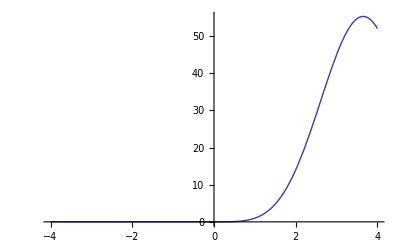

```mathematica
Plot[df[120,z],{z,-4,4}]
```

```mathematica
FullSimplify[Sum[dfa[j,z]dfa[120/j,y],{j,Divisors[120]}]]
```

((720 z^2 (1+3 z)-y^5 (-1+z) z (20+z (-25+9 z))+4 y z^2 (2589+z (-1358+5 (-24+z) z))-y^4 (-1+z) z (-480+z (586+z (-215+9 z)))+y^2 (720+z (10356+z (-13300+z (2355+(1066-45 z) z))))+y^3 (2160+z (-5432+z (2355+z (1252+z (-801+34 z)))))) Sin[π y] Sin[π z])/(π^2 (-5+y) (-4+y) (-3+y) (-2+y) (-1+y) y (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z)

```mathematica
Limit[Limit[((720 z^2 (1+3 z)-y^5 (-1+z) z (20+z (-25+9 z))+4 y z^2 (2589+z (-1358+5 (-24+z) z))-y^4 (-1+z) z (-480+z (586+z (-215+9 z)))+y^2 (720+z (10356+z (-13300+z (2355+(1066-45 z) z))))+y^3 (2160+z (-5432+z (2355+z (1252+z (-801+34 z)))))) Sin[π y] Sin[π z])/(π^2 (-5+y) (-4+y) (-3+y) (-2+y) (-1+y) y (-5+z) (-4+z) (-3+z) (-2+z) (-1+z) z),z->2],y->2]
```

52

```mathematica
dfa[120,2+2]
```

52

```mathematica
pl[n_,y_,z_]:={Sum[Binomial[j-1,z-1]Binomial[(n-j)-1,y-1],{j,1,n-1}],Binomial[n-1,y+z-1]}
```

```mathematica
pl[10,5,2]
```

{84,84}

```mathematica
pr[x_,a_,b_]:={x^(a+b-1)/(a+b-1)!,Integrate[ t^(a-1)/(a-1)! (x-t)^(b-1)/(b-1)!,{t,0,x}]}
```

```mathematica
pr[12,1.51I,.5]
```

{-0.124352-1.22808 ⅈ,-0.124352-1.22808 ⅈ}

```mathematica
Sum[Log[x]^(k-1)/(k-1)!,{k,0,Infinity}]
```

x

```mathematica
lr[100,2]
```

283

```mathematica
FI[n_]:=FactorInteger[n];FI[1]:={}
dzeta[j_,s_,z_]:=j^-s Product[(-1)^p[[2]] Binomial[-z,p[[2]]],{p,FI[j]}]
zeta[n_,s_,z_]:=Sum[dzeta[j,s,z],{j,1,n}]
px[n_,k_,a_]:=Sum[Binomial[k,j]lr[n,j+a],{j,0,k}]
```

```mathematica
Binomial[3,-1]
```

0

```mathematica
Limit[D[lr[100,z]/lr[50,z],z],z->0]
```

125/12

```mathematica
N[1+Integrate[a Hypergeometric1F1[1-a,2,-x],{x,0,n}]+Integrate[b Hypergeometric1F1[1-b,2,-x],{x,0,n}] + a b Integrate[Hypergeometric1F1[1-a,2,-x]Hypergeometric1F1[1-b,2,-y],{x,0,n},{y,0,n-x}]/.a->2.2/.b->-3.5I/.n->10.]
```

157.141+268.802 ⅈ

```mathematica
LaguerreL[z,-n]/.z->(2.2+(-3.5I))/.n->10.
```

157.141+268.802 ⅈ

```mathematica
Sum[(t+a-1)!/t!/(a-1)! (x-t+b-1)!/(x-t)!/(b-1)!,{t,0,x}]
```

((-1+a+b+x)!)/((-1+a+b)! x!)

```mathematica
Sum[Pochhammer[a,t]/t! Pochhammer[b,x-t]/(x-t)!,{t,0,x}]
```

((-1+a+b+x)!)/((-1+a+b)! x!)

```mathematica
Pochhammer[a+b,x]/x!
```

Pochhammer[a+b,x]/(x!)

```mathematica
D[LaguerreL[z,-x],x]
```

LaguerreL[-1+z,1,-x]

```mathematica
D[LaguerreL[-z,Log@x],x]/.z->b/.x->u
```

-LaguerreL[-1-b,1,Log[u]]/u

```mathematica
meh[x_,a_,b_]:=1+Integrate[-LaguerreL[-1-a,1,Log[t]]/t,{t,1,x}]+Integrate[-LaguerreL[-1-b,1,Log[t]]/t,{t,1,x}]+Integrate[(-LaguerreL[-1-a,1,Log[t]]/t)(-LaguerreL[-1-b,1,Log[u]]/u),{t,1,x},{u,1,x/t}]
```

```mathematica
N[meh[10.3,2.3,3.]]
```

453.812

```mathematica
LaguerreL[-z,Log@x]/.x->10.3/.z->2.3+3
```

453.812

```mathematica
D[Integrate[-LaguerreL[-1-b,1,Log[t]]/t,{t,1,x}],x]/.b->a
```

ConditionalExpression[(a Hypergeometric1F1[1+a,2,Log[x]])/x,0≤Re[x]≤ⅇ||x∉Reals]

```mathematica
D[Integrate[(-LaguerreL[-1-a,1,Log[t]]/t)(-LaguerreL[-1-b,1,Log[u]]/u),{t,1,x},{u,1,x/t}],x]
```

∫_1^x (a b Hypergeometric1F1[1+a,2,Log[t]] Hypergeometric1F1[1+b,2,Log[x/t]])/(t x)ⅆt

```mathematica
mee[x_,a_,b_]:=(a Hypergeometric1F1[1+a,2,Log[x]])/x+(b Hypergeometric1F1[1+b,2,Log[x]])/x+∫_1^x (a b Hypergeometric1F1[1+a,2,Log[t]] Hypergeometric1F1[1+b,2,Log[x/t]])/(t x)ⅆt
```

```mathematica
D[LaguerreL[-(a+b),Log@x],x]
```

-LaguerreL[-1-a-b,1,Log[x]]/x

```mathematica
-LaguerreL[-1-a-b,1,Log[x]]/x/.x->11./.a->2/.b->-3.3
```

-0.0579115

```mathematica
N@mee[11.,2,-3.3]
```

-0.0579115

```mathematica
D[(1+x)^(a+b),x]
```

(a+b) (1+x)^(-1+a+b)

```mathematica
D[Integrate[a t^(a-1) b u^(b-1),{t,0,x},{u,0,x}],x]
```

ConditionalExpression[(a+b) x^(-1+a+b),Re[a]>0]

```mathematica
FullSimplify[1+Integrate[a(1+t)^(a-1),{t,0,x}]+Integrate[b(1+u)^(b-1),{u,0,x}]+Integrate[ a(1+t)^(a-1) b (1+u)^(b-1),{t,0,x},{u,0,x}]]
```

ConditionalExpression[(1+x)^(a+b),Re[x]≥-1||x∉Reals]

```mathematica
D[(1+t)^a,t]
```

a (1+t)^(-1+a)

```mathematica
1+Integrate[a (1+t)^(-1+a),{t,0,x}]
```

ConditionalExpression[(1+x)^a,Re[x]≥-1||x∉Reals]

```mathematica
1+3 x+3 x^2+x^3/.x->3
```

64

```mathematica
1+Integrate[a(1+t)^(a-1),{t,0,x}]
```

ConditionalExpression[(1+x)^a,Re[x]≥-1||x∉Reals]

```mathematica
Integrate[ a(1+t)^(a-1) b (1+u)^(b-1),{t,0,x},{u,0,x}]
```

ConditionalExpression[(-1+(1+x)^a) (-1+(1+x)^b),Re[x]≥-1||x∉Reals]

```mathematica
D[(1+x)^(a+b),x]
```

(a+b) (1+x)^(-1+a+b)

```mathematica
D[Integrate[ a(1+t)^(a-1),{t,0,x}],x]
```

ConditionalExpression[a (1+x)^(-1+a),Re[x]≥-1||x∉Reals]

```mathematica
FullSimplify@D[Integrate[ a(1+t)^(a-1) b (1+u)^(b-1),{t,0,x},{u,0,x}],x]
```

ConditionalExpression[b (1+x)^(-1+b) (-1+(1+x)^a)+a (1+x)^(-1+a) (-1+(1+x)^b),Re[x]≥-1||x∉Reals]

```mathematica
D[a(1+t)^(a-1) b (1+u)^(b-1),x]
```

0

```mathematica
b (1+x)^(-1+b) (-1+(1+x)^a)+a (1+x)^(-1+a) (-1+(1+x)^b)/.x->3.3/.a->2.2/.b->1.1
```

80.5758

```mathematica
Integrate[a(1+t)^(a-1) b(1+u)^(b-1)+a(1+u)^(a-1) b(1+t)^(b-1),{t,0,x},{u,0,t}]/.x->3.3/.a->2.2/.b->1.1
```

94.4248

```mathematica
(a+b) (1+x)^(-1+a+b)-a(1+x)^(a-1)-b(1+x)^(b-1)/.x->3.3/.a->2.2/.b->1.1
```

80.5758

```mathematica
Expand[b (1+x)^(-1+b) (-1+(1+x)^a)+a (1+x)^(-1+a) (-1+(1+x)^b)]
```

-a (1+x)^(-1+a)-b (1+x)^(-1+b)+a (1+x)^(-1+a+b)+b (1+x)^(-1+a+b)

```mathematica
Integrate[a(1+t)^(a-1) b(1+u)^(b-1)+a(1+u)^(a-1) b(1+t)^(b-1),{u,0,t}]
```

ConditionalExpression[-a (1+t)^(-1+a)-b (1+t)^(-1+b)+(a+b) (1+t)^(-1+a+b),Re[t]≥-1||t∉Reals]

```mathematica
Integrate[-a(1+t)^(a-1) b(1+t)^(b-1),{t,0,x}]
```

ConditionalExpression[-a b (-1/(-1+a+b)+(1+x)^(-1+a+b)/(-1+a+b)),Re[x]≥-1||x∉Reals]

```mathematica
Integrate[ a(1+t)^(a-1) b (1+u)^(b-1),{t,0,x},{u,0,x}]/.x->3.3/.a->2.2/.b->1.1
```

94.4248

```mathematica
Integrate[a(1+t)^(a-1) b(1+u)^(b-1)+a(1+u)^(a-1) b(1+t)^(b-1),{u,0,t}]/.t->x
```

ConditionalExpression[-a (1+x)^(-1+a)-b (1+x)^(-1+b)+(a+b) (1+x)^(-1+a+b),Re[x]≥-1||x∉Reals]

```mathematica
-a (1+x)^(-1+a)-b (1+x)^(-1+b)+(a+b) (1+x)^(-1+a+b)/.x->3.3/.a->2.2/.b->1.1
```

80.5758

```mathematica
(a+b)(1+x)^(a+b-1)/.x->3.3/.a->2.2/.b->1.1
```

94.513

```mathematica
a(1+x)^(a-1)+b(1+x)^(b-1)+(b (1+x)^(-1+b) (-1+(1+x)^a)+a (1+x)^(-1+a) (-1+(1+x)^b))/.x->3.3/.a->2.2/.b->1.1
```

94.513

```mathematica
a(1+x)^(a-1)+b(1+x)^(b-1)+(-a (1+x)^(-1+a)-b (1+x)^(-1+b)+(a+b) (1+x)^(-1+a+b))/.x->3.3/.a->2.2/.b->1.1
```

94.513

```mathematica
a(1+x)^(a-1)+b(1+x)^(b-1)+Integrate[a(1+x)^(a-1) b(1+u)^(b-1)+a(1+u)^(a-1) b(1+x)^(b-1),{u,0,x}]
```

ConditionalExpression[(a+b) (1+x)^(-1+a+b),Re[x]≥-1||x∉Reals]

```mathematica
D[(1+x)^a,x]+D[(1+x)^b,x]+Integrate[D[(1+x)^a,x] D[(1+u)^b,u]+D[(1+u)^a,u]D[(1+x)^b,x],{u,0,x}]
```

ConditionalExpression[(a+b) (1+x)^(-1+a+b),Re[x]≥-1||x∉Reals]

```mathematica
1+Integrate[(a+b) (1+x)^(-1+a+b),{x,0,n}]
```

ConditionalExpression[(1+n)^(a+b),Re[n]≥-1||n∉Reals]

```mathematica
bla[x_]:=Table[Binomial[t-1,a-1]Binomial[(x-t)-1,b-1],{t,1,x-1}]
bla2[x_,a_,b_]:=Table[Binomial[t-1,a-1]Binomial[(x-t)-1,b-1],{t,1,x-1}]
bla3[x_,a_,b_]:=Sum[Binomial[t-1,a-1]Binomial[(x-t)-1,b-1],{t,1,x-1}]
```

```mathematica
Sum[Binomial[t-1,a-1]Binomial[u-1,b-1],{t,1,x},{u,1,x-t}]
```

∑_(t=1)^x ∑_(u=1)^(-t+x) Binomial[-1+t,-1+a] Binomial[-1+u,-1+b]

```mathematica
Binomial[5,3+2]
```

1

```mathematica
bla2[6,2,2]//TableForm
```

0
3
4
3
0

```mathematica
Binomial[11-1,3+2-1]
```

210

```mathematica
bla3[11,3,2]
```

210

```mathematica
FullSimplify[(1/Gamma[z]/Gamma[1-z]) Sum[(-1)^k/(z-k)Binomial[x,k],{k,0,Infinity}]]
```

Gamma[1+x]/(Gamma[1+x-z] Gamma[1+z])

```mathematica
D[Integrate[1/t LaguerreL[-a-1,1,Log[t]] 1/u LaguerreL[-b-1,1,Log[u]],{t,1,x},{u,1,x/t}],x]
```

∫_1^x (a b Hypergeometric1F1[1+a,2,Log[t]] Hypergeometric1F1[1+b,2,Log[x/t]])/(t x)ⅆt

```mathematica
Integrate[1/t LaguerreL[-a-1,1,Log[t]] 1/u LaguerreL[-b-1,1,Log[u]],{t,1,x},{u,1,x/t}]
```

∫_1^x (a Hypergeometric1F1[1+a,2,Log[t]] (-1+Hypergeometric1F1[b,1,Log[x/t]]))/t ⅆt